```mathematica
eq1[a_, b_, c_, t_] :=a t^3+b t^2 + c t;
```

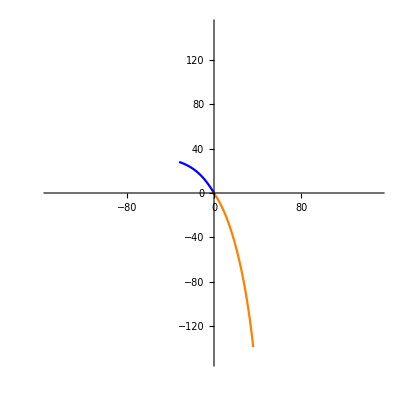

```mathematica
p1 = ParametricPlot[{eq1[-8, 0, -24, t], eq1[-2 ,-8, 38, t]}, {t,0,1}, PlotStyle->Blue, AspectRatio->1, PlotRange -> {{-150,150},{-150,150}}];
p2 = ParametricPlot[{eq1[-46, 99, -17, t], eq1[-99 ,-50, 10, t]}, {t,0,1}, PlotStyle->Orange, AspectRatio->1, PlotRange -> Full];
Show[p1, p2]
```

```mathematica
|
```